```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]


pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]

Needs["VariationalMethods`"]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 332 Kb

{Utilities`CleanSlate`,TriangleLink`,CompiledFunctionTools`,IPOPTLink`,VariationalMethods`,DocumentationSearch`,ResourceLocator`,System`,Global`,Graphics`Mesh`,Graphics`PolygonUtils`}

```mathematica
(* Insert references to similar problems *)
```

```mathematica
Clear[r1]
r1 = { l1 Sin[θ1[t]] , -l1 Cos[θ1[t]] }
```

{l1 Sin[θ1[t]],-l1 Cos[θ1[t]]}

```mathematica
D[r1, t]
```

{l1 Cos[θ1[t]] θ1'[t],l1 Sin[θ1[t]] θ1'[t]}

```mathematica
D[r1, t] . D[r1, t]
```

l1^2 Cos[θ1[t]]^2 θ1'[t]^2+l1^2 Sin[θ1[t]]^2 θ1'[t]^2

```mathematica
D[r1, t] . D[r1, t]  // Expand
```

l1^2 Cos[θ1[t]]^2 θ1'[t]^2+l1^2 Sin[θ1[t]]^2 θ1'[t]^2

```mathematica
D[r1, t] . D[r1, t]  // Expand  // Simplify
```

l1^2 θ1'[t]^2

```mathematica
Clear[T1]
T1  = 1/2 m1 ( D[r1, t] . D[r1, t]  // Expand  // Simplify  )
```

1/2 l1^2 m1 θ1'[t]^2

```mathematica
Clear[r2]
r2 =  r1 + { l2 Sin[θ2[t]] , -l2 Cos[θ2[t]] }
```

{l1 Sin[θ1[t]]+l2 Sin[θ2[t]],-l1 Cos[θ1[t]]-l2 Cos[θ2[t]]}

```mathematica
D[r2, t]
```

{l1 Cos[θ1[t]] θ1'[t]+l2 Cos[θ2[t]] θ2'[t],l1 Sin[θ1[t]] θ1'[t]+l2 Sin[θ2[t]] θ2'[t]}

```mathematica
D[r2, t] . D[r2, t]
```

(l1 Cos[θ1[t]] θ1'[t]+l2 Cos[θ2[t]] θ2'[t])^2+(l1 Sin[θ1[t]] θ1'[t]+l2 Sin[θ2[t]] θ2'[t])^2

```mathematica
D[r2, t] . D[r2, t] // Expand
```

l1^2 Cos[θ1[t]]^2 θ1'[t]^2+l1^2 Sin[θ1[t]]^2 θ1'[t]^2+2 l1 l2 Cos[θ1[t]] Cos[θ2[t]] θ1'[t] θ2'[t]+2 l1 l2 Sin[θ1[t]] Sin[θ2[t]] θ1'[t] θ2'[t]+l2^2 Cos[θ2[t]]^2 θ2'[t]^2+l2^2 Sin[θ2[t]]^2 θ2'[t]^2

```mathematica
D[r2, t] . D[r2, t] // Expand  // Simplify
```

l1^2 θ1'[t]^2+2 l1 l2 Cos[θ1[t]-θ2[t]] θ1'[t] θ2'[t]+l2^2 θ2'[t]^2

```mathematica
Clear[T2]
T2 = 1/2 m2 ( D[r2, t] . D[r2, t] // Expand  // Simplify  )
```

1/2 m2 (l1^2 θ1'[t]^2+2 l1 l2 Cos[θ1[t]-θ2[t]] θ1'[t] θ2'[t]+l2^2 θ2'[t]^2)

```mathematica
Clear[T]
T = T1 + T2
```

1/2 l1^2 m1 θ1'[t]^2+1/2 m2 (l1^2 θ1'[t]^2+2 l1 l2 Cos[θ1[t]-θ2[t]] θ1'[t] θ2'[t]+l2^2 θ2'[t]^2)

```mathematica
Clear[V]
V =  m1 g r1[[2]] + m2 g r2[[2]]// Simplify
```

-g (l1 (m1+m2) Cos[θ1[t]]+l2 m2 Cos[θ2[t]])

```mathematica
Clear[ℒ]
ℒ = T - V ;
ℒ // pdConv
```

g (l1 (m1+m2) cos(θ1(t))+l2 m2 cos(θ2(t)))+1/2 m2 (l1^2 ((∂θ1(t))/(∂t))^2+2 l1 l2 (∂θ1(t))/(∂t) (∂θ2(t))/(∂t) cos(θ1(t)-θ2(t))+l2^2 ((∂θ2(t))/(∂t))^2)+1/2 l1^2 m1 ((∂θ1(t))/(∂t))^2

```mathematica
Clear[q]
q = { θ1[t] , θ2[t] }
```

{θ1[t],θ2[t]}

```mathematica
D[ D[ ℒ , D[q[[1]], t] ] , t ]  - D[ ℒ , q[[1]] ]
D[ D[ ℒ , D[q[[2]], t] ] , t ]  - D[ ℒ , q[[2]] ]
```

g l1 (m1+m2) Sin[θ1[t]]+l1 l2 m2 Sin[θ1[t]-θ2[t]] θ1'[t] θ2'[t]+l1^2 m1 θ1''[t]+1/2 m2 (-2 l1 l2 Sin[θ1[t]-θ2[t]] (θ1'[t]-θ2'[t]) θ2'[t]+2 l1^2 θ1''[t]+2 l1 l2 Cos[θ1[t]-θ2[t]] θ2''[t])

g l2 m2 Sin[θ2[t]]-l1 l2 m2 Sin[θ1[t]-θ2[t]] θ1'[t] θ2'[t]+1/2 m2 (-2 l1 l2 Sin[θ1[t]-θ2[t]] θ1'[t] (θ1'[t]-θ2'[t])+2 l1 l2 Cos[θ1[t]-θ2[t]] θ1''[t]+2 l2^2 θ2''[t])

```mathematica
Table[
D[ D[ ℒ , D[q[[i]], t] ] , t ]  - D[ ℒ , q[[i]] ] ,
{ i , 1, 2 } ] //Simplify //  TableForm
```

l1 (g m1 Sin[θ1[t]]+g m2 Sin[θ1[t]]+l2 m2 Sin[θ1[t]-θ2[t]] θ2'[t]^2+l1 (m1+m2) θ1''[t]+l2 m2 Cos[θ1[t]-θ2[t]] θ2''[t])
l2 m2 (g Sin[θ2[t]]-l1 Sin[θ1[t]-θ2[t]] θ1'[t]^2+l1 Cos[θ1[t]-θ2[t]] θ1''[t]+l2 θ2''[t])

```mathematica
Clear[eqs]
eqs = 
EulerEquations[ ℒ , q , t ] ;
eqs // TableForm
```

-l1 (g m1 Sin[θ1[t]]+g m2 Sin[θ1[t]]+l2 m2 Sin[θ1[t]-θ2[t]] θ2'[t]^2+l1 (m1+m2) θ1''[t]+l2 m2 Cos[θ1[t]-θ2[t]] θ2''[t])==0
-l2 m2 (g Sin[θ2[t]]-l1 Sin[θ1[t]-θ2[t]] θ1'[t]^2+l1 Cos[θ1[t]-θ2[t]] θ1''[t]+l2 θ2''[t])==0

```mathematica
Clear[parameters]
parameters = { 
g-> 9.8 ,
l1 -> 0.5 ,
l2 -> 0.8 ,
m1 -> 2 ,
m2-> 4 
} ;
parameters // TableForm
```

g→9.8
l1→0.5
l2→0.8
m1→2
m2→4

```mathematica
eqs /. parameters // Expand // TableForm
```

-29.4 Sin[θ1[t]]-1.6 Sin[θ1[t]-θ2[t]] θ2'[t]^2-1.5 θ1''[t]-1.6 Cos[θ1[t]-θ2[t]] θ2''[t]==0
-31.36 Sin[θ2[t]]+1.6 Sin[θ1[t]-θ2[t]] θ1'[t]^2-1.6 Cos[θ1[t]-θ2[t]] θ1''[t]-2.56 θ2''[t]==0

```mathematica
Clear[ics]
ics = { 
θ1[0] == 0.1 ,
θ1'[0] == 0 ,
θ2[0] == 0.1 ,
θ2'[0] == 0 
} ;
ics // TableForm
```

θ1[0]==0.1
θ1'[0]==0
θ2[0]==0.1
θ2'[0]==0

```mathematica
Clear[solution]
solution[t_] = 
First[NDSolve[ Union[ eqs /. parameters , ics ] , q , { t, 0, 300 } ]]
```

{θ1[t]→InterpolatingFunction[…][t],θ2[t]→InterpolatingFunction[…][t]}

```mathematica
Plot[ Evaluate[ q /. solution[t]]  , { t, 0, 10 } , PlotLabels-> q ]
```

-Graphics-

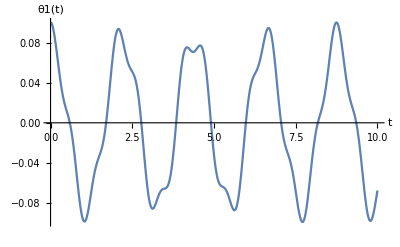

```mathematica
Plot[ Evaluate[ q[[1]] /. solution[t]]  , { t, 0, 10 } , AxesLabel-> { t , q[[1]] } ]
```

```mathematica
Animate[ 
ParametricPlot[ { solution[t][[1,2]] , solution'[t][[1,2]] } , { t , 0, tmax } , AxesLabel-> { q[[1]] , D[q[[1]], t] } ]  ,
{ tmax , 1 ,100 , 0.5  } ]
```

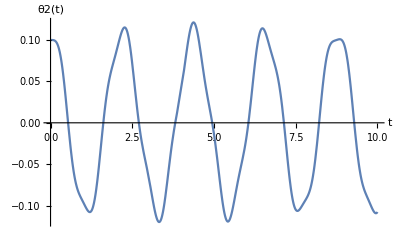

```mathematica
Plot[ Evaluate[ q[[2]] /. solution[t]]  , { t, 0, 10 } , AxesLabel-> { t , q[[2]] } ]
```

```mathematica
Animate[ 
ParametricPlot[ { solution[t][[2,2]] , solution'[t][[2,2]] } , { t , 0, tmax } , AxesLabel-> { q[[1]] , D[q[[1]], t] } ]  ,
{ tmax , 1 ,100 , 0.5  } ]
```